```mathematica
Quit[]
```

```mathematica
(*Index of refraction, Rayleigh scattering length, and Sellmeier coefficients in solid and liquid argon and xenon*)

a0 = 1.24;
aUV = 0.27;
aIR = 0.00047;
xUV = 106.6;
xIR = 908.3;
ncalc[x_] := √(a0 + (aUV*x^2)/(x^2 - xUV^2)+(aIR*x^2)/(x^2 - xIR^2));
```

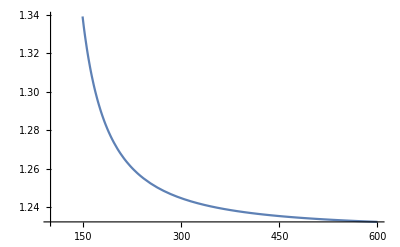

```mathematica
Plot[ncalc[x], {x, 100, 600}]
```

```mathematica
ncalc[128]
```

1.45641

```mathematica
kT = 2.18*10^-9;
kB = 1.380649*10^-23   ;
T = 83.81;
```

```mathematica
lray[x_] := 1/((8*Pi^3)/(3*x^4) *(((ncalc[x*10^9]*ncalc[x*10^9]-1)*(ncalc[x*10^9]*ncalc[x*10^9]+2))/3)^2*kB*T*kT);
```

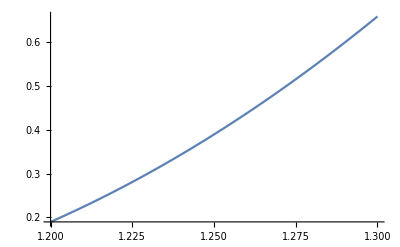

```mathematica
Plot[lray[x], {x, 1.2*10^-7, 1.3*10^-7}]
```

```mathematica
lray[128*10^-9]
```

0.542612

```mathematica
lray_mid= 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((ncalc[128]*ncalc[128]-1)*(ncalc[128]*ncalc[128]+2))/3)^2*kB*T*kT)
lray_up= 1/((8*Pi^3)/(3*(128*10^-9)^4) *(1/3((ncalc[128]+0.07)*(ncalc[128]+0.07)-1)*((ncalc[128]+0.07)*(ncalc[128]+0.07)+2))^2*kB*T*kT)
lray_down = 1/((8*Pi^3)/(3*(128*10^-9)^4) *(1/3((ncalc[128]-0.07)*(ncalc[128]-0.07)-1)*((ncalc[128]-0.07)*(ncalc[128]-0.07)+2))^2*kB*T*kT)
```

0.542612

0.349314

0.88553

```mathematica
nmid = ncalc[128]
nup = √((a0+0.09) + ((aUV+0.09)*128^2)/(128^2 - xUV^2)+((aIR+0.007)*128^2)/(128^2 - xIR^2))
ndown = √((a0-0.09) + ((aUV-0.09)*128^2)/(128^2 - xUV^2)+((aIR-0.007)*128^2)/(128^2 - xIR^2))
```

1.45641

1.58262

1.31816

```mathematica
lraymid= 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((nmid*nmid-1)*(nmid*nmid+2))/3)^2*kB*T*kT)
lraydown = 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((nup*nup-1)*(nup*nup+2))/3)^2*kB*T*kT)
lrayup = 1/((8*Pi^3)/(3*(128*10^-9)^4) *(((ndown*ndown-1)*(ndown*ndown+2))/3)^2*kB*T*kT)
```

0.542612

0.252117

1.52428

```mathematica
(*对折射率拟合公式求导计算误差*)
a10 = 1.24;
a20 = 0.27;
a30 = 0.00047;
a10err = 0.09;
a20err = 0.09;
a30err = 0.007;
Fray[a1, a2, a3] := √(a1 + (a2*128^2)/(128^2-106.6^2)+(a3*128^2)/(128^2-908.3^2));
D[Fray[a1, a2, a3], a1]
D[Fray[a1, a2, a3], a2]
D[Fray[a1, a2, a3], a3]
```

1/(2 √(a1+3.26346 a2-0.0202616 a3))

1.63173/(√(a1+3.26346 a2-0.0202616 a3))

-0.0101308/(√(a1+3.26346 a2-0.0202616 a3))

```mathematica
Frayerr = √((a10err/(2 √(a10+3.263458979691023 a20-0.0202615578652297 a30)))^2+((1.6317294898455115*a20err)/(√(a10+3.263458979691023 a20-0.0202615578652297 a30)))^2+(-(0.01013077893261485*a30err)/(√(a10+3.263458979691023 a20-0.0202615578652297 a30)))^2)
```

```mathematica
0.10546188244831425


(*Grace用到的LAr三相点折射率数据：1969 --> Root TF1 Fitting*)
```

```mathematica
(*Index of refraction, Rayleigh scattering length, and Sellmeier coefficients in solid and liquid argon and xenon*)

a0fit = 1.12;
aUVfit = 0.11;
aIRfit = 0.00026;
ncalcfit[x_] := √(a0fit + (aUVfit*x^2)/(x^2 - xUV^2)+(aIRfit*x^2)/(x^2 - xIR^2));
```

```mathematica
ncalcfit[128]
```

1.21613